# Edge-smoothing algorithms: PSim preprocessing for confinement geometries

## NOTEBOOK LOG:

07/15/2015 -- Copied from phase-field notebook

```mathematica
{$Version, $ReleaseNumber, $LicenseID}
```

{8.0 for Mac OS X x86 (64-bit) (February 23, 2011),1,L3270-5626}

## Modules

```mathematica
<<"/Users/ssides/hpc-devel/ssides/mathematica/mathModules/sides.m";
```

```mathematica
?helpTx
```

List of homemade modules in "tx.m"
    memuse
    rdist
    getColumns
    dropColumns
    cullList
    readFile
    writeFile
    writeLines
    readH5File
    directionCosines
    generateLineOut

 For more information type "? command " for help on "command"

### Common plot options

```mathematica
Needs["PlotLegends`"]
```

```mathematica
pltDens[data_,linePts_List:{}]:=
Module[
{linesOut,plt},

(* Set graphics objects *)
linesOut =Line[linePts];

plt = ListDensityPlot[data,
Epilog->{Thick,linesOut},
FrameLabel->{"x","y"},
AspectRatio->1.0,
ColorFunction->"BlueGreenYellow",
PlotRange->{0,1}];

Show[plt]
];
```

```mathematica
legendSize={0.4,0.25};
legendPosition={-0.8,0.3};
plotLegend={
Style["PDMS",20],
Style["H_20",20],
Style["PEO",20]};
fLabel={"r [R_g]","ϕ_species(r)"};
lLabel=Style["species",20];
joined=True;
imageSize=800;
insetFunc[px_]:=Inset[px,{8.0,1.1},{0.5,0.5},5.0];
```

## Prototype algorithms

### Gaussian filtering (arbitrary test)

```mathematica
tst=Table[0.2*x+0.5*Random[],{x,1,10}]
```

{0.390879,0.628321,1.06961,0.806949,1.02959,1.35402,1.77943,2.07439,1.96975,2.12962}

```mathematica
res=GaussianFilter[tst,2]
```

{0.475714,0.668512,0.883916,0.928501,1.09134,1.38423,1.72333,1.95589,2.02423,2.09294}

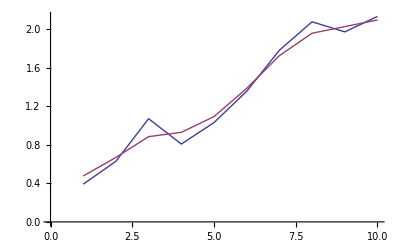

```mathematica
ListLinePlot[{tst,res}]
```

### Gaussian filtering (Step function 1D)

Testing Gaussian Filter on step function. Trial Tanh[] function for comparison. Need to sort out effect of discretization and the width scaling on filter

```mathematica
dx=0.05;
dx2=dx/2.0;
stepDat=Table[2*UnitStep[x]-1,{x,-2,2,dx}];
tanhDat=Table[Tanh[(x+dx2)/0.21],{x,-2,2,dx}];

gausDat4=GaussianFilter[stepDat,4];
gausDat8=GaussianFilter[stepDat,8];
```

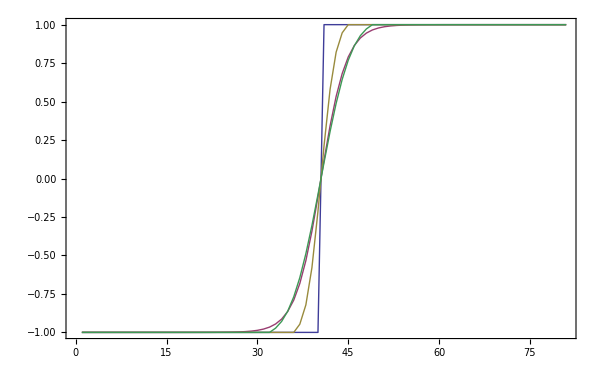

```mathematica
ListLinePlot[{stepDat,tanhDat,gausDat4,gausDat8},
ImageSize->600,Frame->True]
```

### Convolve with Gaussian matrix

#### Equiv between Erf(x) ---> Tanh(x) (using Erf(x) as integral of gaussian)

```mathematica
Clear[σ];
gfunc[x_,x0_,σ_]:=1/(σ*√(2π))Exp[-(x-x0)^2/(2 σ^2)]
```

```mathematica
(* Shows integral of Gaussian to Error function *)
Integrate[gfunc[x,x0,σ],x]
```

1/2 Erf[(x-x0)/(√2 σ)]

NOTE: erf(x) ~ tanh(√π log(2) x)
Showing scaling for Mathematica functions related to Gaussian smoothing

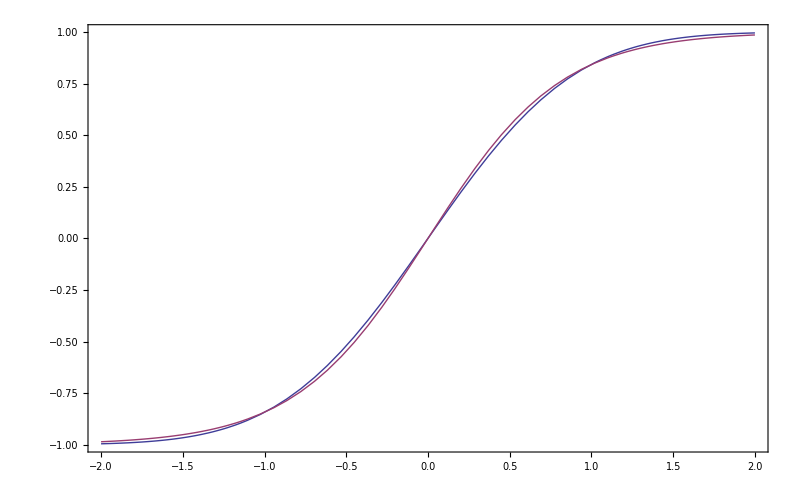

```mathematica
Plot[{Erf[x],Tanh[Log[2] √π*x]},{x,-2,2}]
```

#### GaussianMatrix function specifics

```mathematica
?GaussianMatrix
```

RowBox[{"GaussianMatrix", "[", StyleBox["r", "TI"], "]"}] gives a matrix that corresponds to a Gaussian kernel of radius StyleBox["r", "TI"]. 
RowBox[{"GaussianMatrix", "[", RowBox[{"{", RowBox[{StyleBox["r", "TI"], ",", StyleBox["σ", "TR"]}], StyleBox["}", "TR"]}], "]"}] gives a matrix corresponding to a Gaussian kernel with radius StyleBox["r", "TI"] and standard deviation StyleBox["σ", "TR"].
RowBox[{"GaussianMatrix", "[", RowBox[{StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] gives a matrix formed from the SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]SuperscriptBox["", "th"] derivative of the Gaussian with respect to rows and the SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]SuperscriptBox["", "th"] derivative with respect to columns.
RowBox[{"GaussianMatrix", "[", RowBox[{StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["12", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["21", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["22", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives a matrix formed from the sums of the SubscriptBox[StyleBox["n", "TI"], StyleBox[StyleBox[RowBox[{"i", StyleBox["1", FontSlant -> "Plain"]}]], "TI"]] and SubscriptBox[StyleBox["n", "TI"], StyleBox[StyleBox[RowBox[{"i", StyleBox["2", FontSlant -> "Plain"]}]], "TI"]] derivatives.
RowBox[{"GaussianMatrix", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["σ", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives an array corresponding to a Gaussian kernel with radius SubscriptBox[StyleBox["r", "TI"], StyleBox["i", "TI"]] in the StyleBox["i", "TI"]SuperscriptBox["", "th"] index direction.

Testing equivalence of ListConvolve[GaussianMatrix[]] and GaussianFilter. Still need to sort out format of GaussianMatrix call below (ie not sure what “Fixed” keyword is or the third argument is.

NOTE: the wrap-around value for the ListConvolve call k, is k=r+1 where --> GaussianMatrix[r]
When only one argument, σ=r/2

```mathematica
g20b10=MatrixPlot[GaussianMatrix[ {20,10}]];
g20 =MatrixPlot[GaussianMatrix[20]];
g20b5=MatrixPlot[GaussianMatrix[ {20,5}]];
```

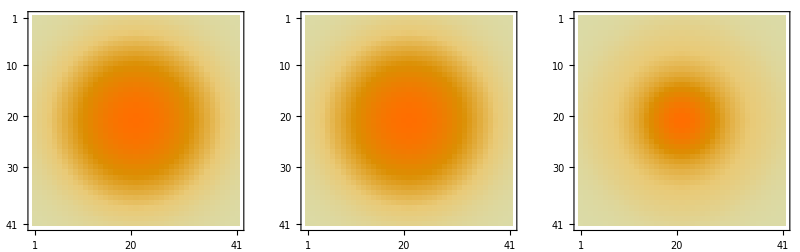

```mathematica
GraphicsGrid[{{g20b10,g20,g20b5}},ImageSize->800]
```

```mathematica
?ListConvolve
```

RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"]}], "]"}] forms the convolution of the kernel StyleBox["ker", "TI"] with StyleBox["list", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["k", "TI"]}], "]"}] forms the cyclic convolution in which the StyleBox["k", "TI"]SuperscriptBox["", "th"] element of StyleBox["ker", "TI"] is aligned with each element in StyleBox["list", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}]}], "]"}] forms the cyclic convolution whose first element contains RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", "1", "]"}], "]"}], RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], "]"}], "]"}]}] and whose last element contains RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", RowBox[{"-", "1"}], "]"}], "]"}], RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]], "]"}], "]"}]}]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["p", "TI"]}], "]"}] forms the convolution in which StyleBox["list", "TI"] is padded at each end with repetitions of the element StyleBox["p", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] forms the convolution in which StyleBox["list", "TI"] is padded at each end with cyclic repetitions of the SubscriptBox[StyleBox["p", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"]}], "]"}] forms a generalized convolution in which StyleBox["g", "TI"] is used in place of Times and StyleBox["h", "TI"] in place of Plus. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"], ",", StyleBox["lev", "TI"]}], "]"}] forms a convolution using elements at level StyleBox["lev", "TI"] in StyleBox["ker", "TI"] and StyleBox["list", "TI"].

NOTE: must set GaussianMatrix parameters so that the length scale is preserved as the width of the kernel is varied.

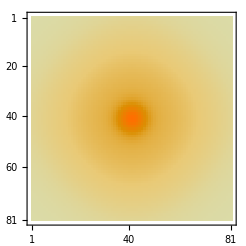

```mathematica
(* Units of length *)
L=2.0;
dx=0.05;
σ=0.2;

(* Converting to number of matrix elements *)
Nx=L/dx;
σnx=σ/dx;

(* Scaling for constant system size *)
MatrixPlot[GaussianMatrix[{Nx,σnx}]]
```

#### Results 1D

```mathematica
(* L, dx and σ can be changed and results are scaled *)
L=1.2; dx=0.025; σ=0.15;

Nx=L/dx; σnx=σ/dx;
L2=L/2.;
dx2=dx/2.0;

(* There a shift of dx2 because of Table[] end effects *)
stepDat=Table[2*UnitStep[x-L2]-1,{x,0,L,dx}];
tanhDat=Table[Tanh[√π Log[2]*(x-L2+dx2)/(σ √2)],{x,0,L,dx}];
erfDat=Table[Erf[(x-L2+dx2)/(√2 σ)],{x,0,L,dx}];

gausDat8=ListConvolve[GaussianMatrix[{{3},σnx}],stepDat,4,"Fixed"];
gausDat8other1=ListConvolve[GaussianMatrix[{{6},σnx}],stepDat,7,"Fixed"];
gausDat8other2=ListConvolve[GaussianMatrix[{{10},σnx}],stepDat,11,"Fixed"];
```

Below: shows how gaussian filtering applied to a step function gives erf functions (which are a good approximation to tanh... see above). The size of the gaussian filter matrix improves the comparison to the analytic result.

As dx and/or σ varies the approx to exact result varies with the size (r) of the Gaussian matrix

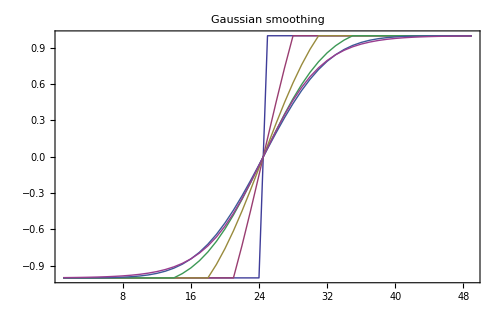

```mathematica
ListLinePlot[{stepDat,gausDat8,gausDat8other1,gausDat8other2,erfDat,tanhDat},
PlotLegend->{"step","gaus r=3","gaus r=6","gaus r=10","erf","~tanh"},
LegendSize->{0.3,0.5},LegendPosition->{-0.7,0.0},
ImageSize->500,Frame->True,
PlotLabel->"Gaussian smoothing",
PlotRange->All]
```

### Gaussian smoothing 2D test

```mathematica
(* Making mask function by-hand *)
Clear[makeMask]
makeMask:=Module[{dx=0.02,xmin=0.2,xmax=0.8,ymin=0.3,ymax=0.7},
val[x_,y_]:=If[((x>xmin)&&(x<xmax) )&& ( (y>ymin)&&(y<ymax)),0,1]; 
Table[Table[val[x,y],{x,0,1,dx}],{y,0,1,dx}]
]
```

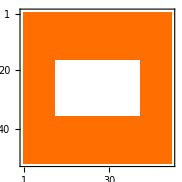

```mathematica
MatrixPlot[makeMask]
```

```mathematica
?GaussianFilter
```

RowBox[{"GaussianFilter", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["r", "TI"]}], "]"}] filters StyleBox["image", "TI"] by convolving with a Gaussian kernel of pixel radius StyleBox["r", "TI"].
RowBox[{"GaussianFilter", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] convolves StyleBox["image", "TI"] with a kernel formed from the SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]]SuperscriptBox["", "th"] derivatives of the discrete Gaussian.
RowBox[{RowBox[{"GaussianFilter", "[", RowBox[{StyleBox["image", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["r", "TI"], ",", StyleBox["σ", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}], " "}] uses a Gaussian kernel with radius StyleBox[RowBox[{"r", " "}], "TI"] and standard deviation StyleBox["σ", "TI"].
RowBox[{"GaussianFilter", "[", RowBox[{StyleBox["image", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] uses radii SubscriptBox[StyleBox["r", "TI"], StyleBox["i", "TI"]] etc. in vertical and horizontal directions.
RowBox[{"GaussianFilter", "[", RowBox[{StyleBox["data", "TI"], ",", StyleBox["…", "TR"]}], "]"}] applies Gaussian filtering to an array of StyleBox["data", "TI"].

```mathematica
Manipulate[
filterMask=GaussianFilter[makeMask,{radius,sigma}];
ListPlot3D[filterMask,
MaxPlotPoints->100,
AxesLabel->{"x","y"},
ImageSize->500],
{sigma,0,2},{radius,1,20}]
```

```mathematica
?ListContourPlot
```

RowBox[{"ListContourPlot", "[", StyleBox["array", "TI"], "]"}] generates a contour plot from an array of height values. 
RowBox[{"ListContourPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] generates a contour plot from values defined at specified points.

```mathematica
sigma=0.0;
filterMask=GaussianFilter[makeMask,{10,sigma}];
p1=ListPlot3D[filterMask,PlotLabel->"raw image",
MaxPlotPoints->80,AxesLabel->{"x","y"},ImageSize->400];
p1c=ListContourPlot[filterMask,MaxPlotPoints->80,ImageSize->400];
```

```mathematica
sigma=0.8;
filterMask=GaussianFilter[makeMask,{10,sigma}];
p2=ListPlot3D[filterMask,PlotLabel->"with edge smoothing",
MaxPlotPoints->80,AxesLabel->{"x","y"},ImageSize->400];
p2c=ListContourPlot[filterMask,MaxPlotPoints->80,ImageSize->400];
```

```mathematica
GraphicsGrid[{{p1,p2},{p1c,p2c}},ImageSize->600]
```

-Graphics-

## Peanut shape vias

```mathematica
(* Making mask function by-hand *)
Clear[makeVias];

makeVias[rc1_List,rc2_List]:=Module[{dx=0.02,radius1=0.2,radius2=0.2},

(* Generates two spheres *)
val[tstPt_]:=If[ 
(rdist[rc1,tstPt] < radius1)||
(rdist[rc2,tstPt] < radius2),
0,1];

 (* Populate table with values from function above *)
Table[Table[val[{x,y}],{x,0,1,dx}],{y,0,1,dx}]
]
```

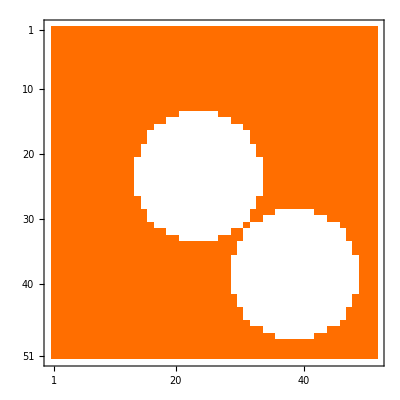

```mathematica
MatrixPlot[makeVias[{0.45,0.45},{0.75,0.75}]]
```

```mathematica
Manipulate[
filterMask=GaussianFilter[makeVias[{0.45,0.45},{0.75,y}],{20,sigma}];
ListPlot3D[filterMask,
MaxPlotPoints->80,
AxesLabel->{"x","y"},
ImageSize->500],
{sigma,0,2},{y,0.2,0.8}]
```

GaussianFilter::arg1: The first argument makeVias[{0.45, 0.45}, {0.75, 0.2}] is neither a rectangular array nor an image.

General::stop: Further output of GaussianFilter :: arg1 will be suppressed during this calculation.

ListPlot3D::arrayerr: GaussianFilter[makeVias[{0.45, 0.45}, {0.75, 0.2}], {20., 0.}] must be a valid array or a list of valid arrays.

```mathematica
sigma=0.0;
filterMask=GaussianFilter[makeVias[{0.45,0.45},{0.75,0.75}],{10,sigma}];
p1=ListPlot3D[filterMask,PlotLabel->"raw image",
MaxPlotPoints->80,AxesLabel->{"x","y"},ImageSize->400];
p1c=ListContourPlot[filterMask,MaxPlotPoints->100,ImageSize->400,Contours->6];
```

```mathematica
sigma=2.0;
filterMask=GaussianFilter[makeVias[{0.45,0.45},{0.75,0.75}],{10,sigma}];
p2=ListPlot3D[filterMask,PlotLabel->"with edge smoothing",
MaxPlotPoints->80,AxesLabel->{"x","y"},ImageSize->400];
p2c=ListContourPlot[filterMask,MaxPlotPoints->100,ImageSize->400,Contours->6];
```

```mathematica
GraphicsGrid[{{p1,p2},{p1c,p2c}},ImageSize->900]
```

-Graphics-

## Import TSMC data

### Import data and visualize

```mathematica
SetDirectory["/Users/ssides/tsmc-litho"]
```

/Users/ssides/tsmc-litho

```mathematica
FileNames[]
```

{1_gkern.png,2_input_data.png,3_filtered_result.png,edgeSmooth.nb,export.jpg,filter.dat,gaussianTest.py,guider.dat,plotAnalysis.py,runjobs.py,runjobs.pyc}

```mathematica
rawDat=readFile["guider.dat",4];
vals = getColumns[rawDat,{4}];
coords= getColumns[rawDat, {1,2,3}];
```

```mathematica
fig=Import["export.jpg",ImageSize->500]
```

-Graphics-

```mathematica
maxVal=Max[vals];
minVal=Min[vals];
numVals= Length[vals];

boxR = {1,1,0.3};
```

```mathematica
Options[ListContourPlot3D];
```

```mathematica
contourVals={0.3};

c1=ListContourPlot3D[rawDat,
Contours->contourVals,SphericalRegion->True,MaxPlotPoints->40,BoxRatios->boxR,
PlotLabel->{"Contours at",contourVals},ViewPoint->{1.39,0.89,-2.95},ViewVertical->{-0.41, -0.126,-3.01},Mesh->5];
```

```mathematica
(* the following is completely another way.try rotating the output of this: 
Row[{Show[c1,ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]],Show[c1,ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]]}]

Dynamic[vp]
Dynamic[vv]*)
```

```mathematica
contourVals={0.06,0.3,0.35,0.5,0.83};

c5=ListContourPlot3D[rawDat,
Contours->contourVals,SphericalRegion->True,MaxPlotPoints->40,BoxRatios->boxR,
PlotLabel->{"Contours at",contourVals},ViewPoint->{1.39,0.89,-2.95},ViewVertical->{-0.41, -0.126,-3.01},Mesh->5];
```

Raw data does not correspond to image from TSMC. (Must be some filtering in the jpg image). TSMC says that above/below threshold value one can consider all exposed or not at all

```mathematica
gg=GraphicsGrid[{{fig,c1,c5}},ImageSize->900]
```

-Graphics-

### Filter data

```mathematica
rawDat=readFile["guider.dat",4];
vals = getColumns[rawDat,{4}];
coords= getColumns[rawDat, {1,2,3}];
```

```mathematica
filterFunc[x_,{lowerT_,upperT_}]:=Module[{tmp=0.0},
If[x <= lowerT, Return[0]];
If[x >=upperT,Return[1]];
If[(x>lowerT) && (x<upperT),Return[x]]
]
```

```mathematica
lowT=0.1;highT=0.4;
filterDat=Map[{#[[1]],#[[2]],#[[3]],filterFunc[#[[4]],{lowT,highT}]}&,rawDat];
```

```mathematica
contourVals={0.2,0.25,0.3};

cFilter=ListContourPlot3D[filterDat,
Contours->contourVals,SphericalRegion->True,MaxPlotPoints->40,BoxRatios->boxR,
PlotLabel->{"Contours at",contourVals},ViewPoint->{1.39,0.89,-2.95},ViewVertical->{-0.41, -0.126,-3.01},Mesh->5,ImageSize->600];
```

```mathematica
GraphicsGrid[{{fig,cFilter}},ImageSize->900]
```

-Graphics-

### Read filter data from Python code

```mathematica
newDat=readFile["filter.dat",4];
```

```mathematica
contourVals={0.2,0.25,0.3};

cFilter=ListContourPlot3D[newDat,
Contours->contourVals,SphericalRegion->True,MaxPlotPoints->40,BoxRatios->boxR,
PlotLabel->{"Contours at",contourVals},ViewPoint->{1.39,0.89,-2.95},ViewVertical->{-0.41, -0.126,-3.01},Mesh->5,ImageSize->600];
```

```mathematica
GraphicsGrid[{{fig,cFilter}},ImageSize->900]
```

-Graphics-